```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test.dat"];
```

```mathematica
data1=Transpose[data][[1]];
data2=Transpose[data][[2]];
ratio=data1/data2;
```

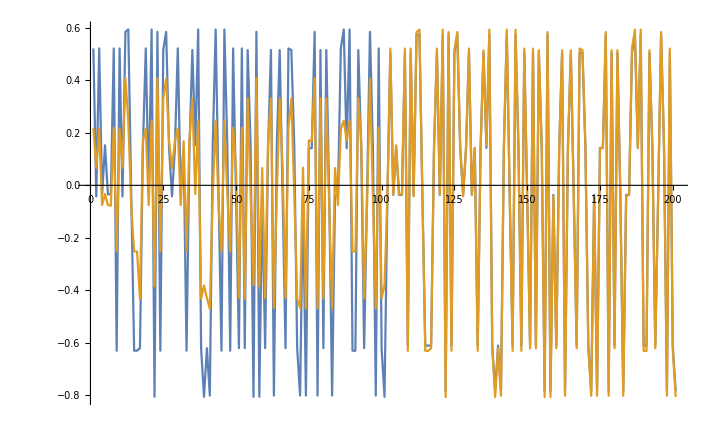

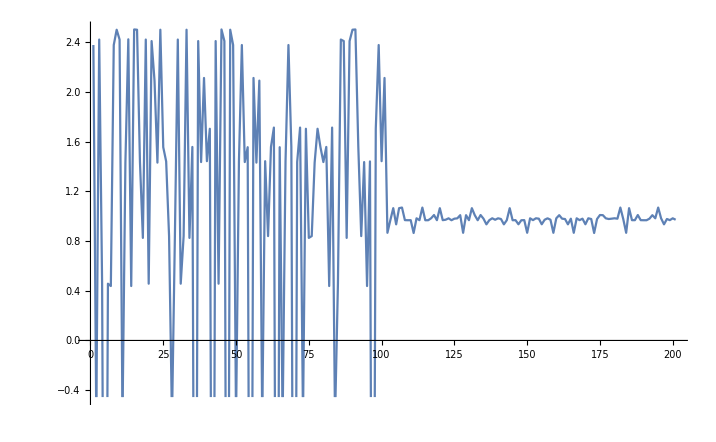

```mathematica
ListPlot[{data1,data2},Joined->True]
ListPlot[ratio,Joined->True]
```

```mathematica
n=2;
data1[[n]]/data2[[n]]
ratio[[n]]
```

-0.639586

-0.639586